## Plot Routine

```mathematica
PlotEquilibriumMeasure[V_,opts:OptionsPattern[]]:=Module[{supp,x,ψ},
supp=EquilibriumMeasureSupport[V,{-1,1}];
ψ[x_]=EquilibriumMeasure[V,supp,x];
Plot[ψ[x],{x,supp⟦1⟧,supp⟦2⟧},opts]];
```

## Nice Examples

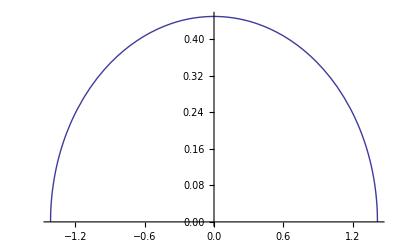

```mathematica
V[x_]:=x^2;
PlotEquilibriumMeasure[V]
```

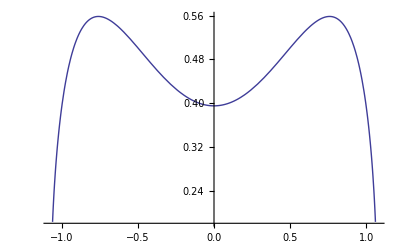

```mathematica
V[x_]:=x^4;
PlotEquilibriumMeasure[V]
```

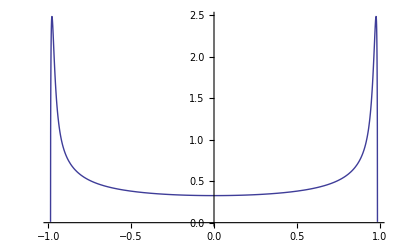

```mathematica
V[x_]:=x^100;
PlotEquilibriumMeasure[V,PlotRange->All]
```

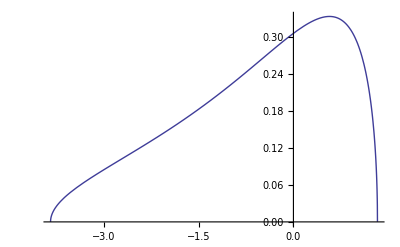

```mathematica
V[x_]:=Exp[x]-x;
PlotEquilibriumMeasure[V]
```

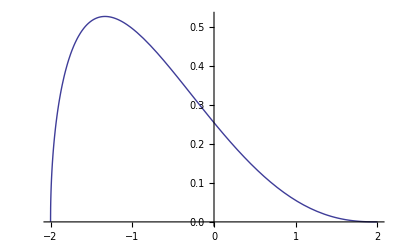

```mathematica
V[x_]:=x^2/5-4/15 x^3+x^4/20+8/5 x;
PlotEquilibriumMeasure[V]
```

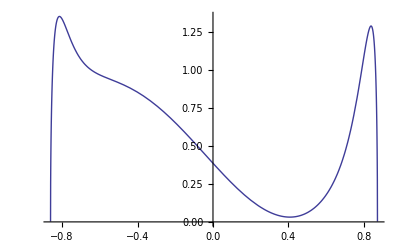

```mathematica
V[x_]:=Sin[3 x] + 10 x^20;
PlotEquilibriumMeasure[V]
```

## Wishart

```mathematica
V[x_]:=x-0.5 Log[x]
```

```mathematica
supp=EquilibriumMeasureSupport[V,{.01,1.}]
```

{0.0505103,4.94949}

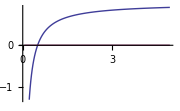

```mathematica
Vp=IFun[V',Line[supp]]
```

```mathematica
ψ[x_]:=-1/(2 π)HilbertInverse[Vp,x];
```

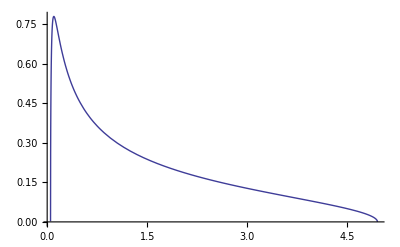

```mathematica
Plot[ψ[x],{x,supp⟦1⟧,supp⟦2⟧}]
```